## Final Plot of Bootstrapped EWS for Ricker undergoing Flip

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/fisheries"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,30,10,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
bl=0.5;
bh=2.3; (* realisation nuber for individual trajectory and power spectrum evolution *)
rw=0.4; (* rolling window *)
```

## Import Data

```mathematica
(* Job number *)
jobNum=5923;
```

```mathematica
(* Data directory *)
dataDir="hagrid/ricker_bootstrap/Jobs/job-"<>ToString[jobNum]<>"/flip/";
```

```mathematica
(* Import parameters used *)
pars=Import[dataDir<>"../pars.txt","Data"];
(* Assign relevant parameters *)
rw=pars[[2,Position[pars,"rw"][[1,2]]]];
```

```mathematica
(* Import original EWS *)
ewsStd=Import[dataDir<>"ews_orig.csv"];

(* Import original power spectrum data *)
specData=Import[dataDir<>"pspec_orig.csv"];

(* Import bootrapped EWS (intervals) *)
ewsBoot=Import[dataDir<>"ews_intervals.csv"];

(* Import bootrapped spectrum (for one sample) *)
specDataBoot=Import[dataDir<>"pspec_boot.csv"];
```

```mathematica
pars
```

{{tmax,seed,sigma,span,rw,ham_length,ham_offset,sweep,block_size,bs_type,n_samples},{1000,2,0.04,0.5,0.4,40,0.5,true,20,Stationary,100}}

```mathematica
pars//TableForm
```

tmax | seed | sigma | span | rw | ham_length | ham_offset | sweep | block_size | bs_type | n_samples
1000 | 2 | 0.04 | 0.5 | 0.4 | 40 | 0.5 | true | 20 | Stationary | 100

## Trajectory Plots

```mathematica
ewsStd[[1]]
```

{,Time,State variable,Smoothing,Residuals,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Params fold,Params hopf,Params null,Smax,Smax/Var}

```mathematica
(* Extract info *)
tVals = ewsStd[[2;;,2]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
xVals = ewsStd[[2;;,3]];
```

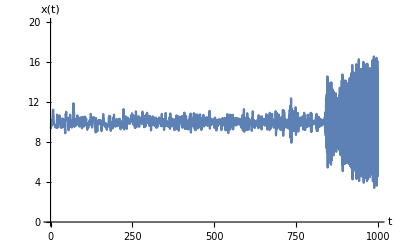

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[xVals,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},{0,20}}]
```

## Bifurcation Diagram (truncated growth)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
(* Import data *)
rawdata=Import["bifurcation/fish_trun.dat"];
(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{1lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of r *)
rbifVals=fulldata[[;;,1]];
tbifVals=(rbifVals-bl)*tmax /(bh-bl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections[[8]]=Cases[nodeSections[[8]],{x_,_,_,_}/; x<999] ; 
nodeSections[[10]]=Cases[nodeSections[[10]],{x_,_,_,_}/; x<999];
(* had to seperate out branches for plotting purposes *)
```

```mathematica
(* remove empty nodesections *)
nodeSections=DeleteCases[nodeSections,{}];
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
numBranches
```

8

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1,2,1,2,2}

```mathematica
(* Take relevant branches of node sections *)
delList={5,7};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4,6,8}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

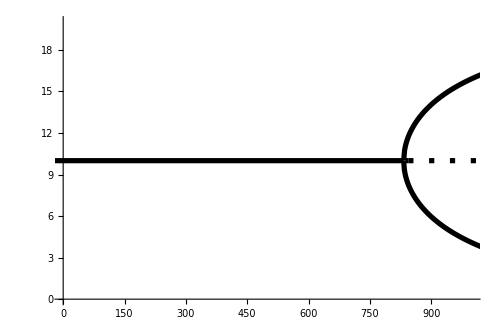

```mathematica
(* Make plot *)
bifPlotTrun=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

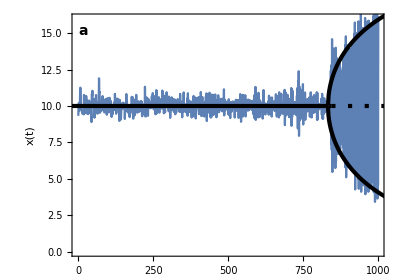

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotTrun},
PlotRange->{{0,tmax},{0,16}},
LabelStyle->14,
AspectRatio->0.7,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## EWS Plots

### Variance

```mathematica
indexStd=Position[ewsStd[[1]],"Variance"][[1,1]];
indexBoot = Position[ewsBoot[[1]],"Variance"][[1,1]];
```

```mathematica
ewsBoot[[1]]
```

{Time,,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Smax}

```mathematica
Flatten[Position[ewsBoot[[;;,2]],0.05]]
```

{}

```mathematica
(* Extract confidence intervals *)
lowerSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Lower",_}][[;;,{1,3}]];
upperSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Upper",_}][[;;,{1,3}]];
meanSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Mean",_}][[;;,{1,3}]];
```

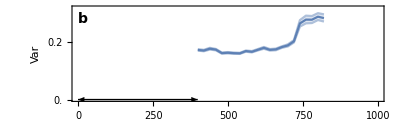

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=0;
ymax=0.32;
plotVar=ListLinePlot[{lowerSeries,upperSeries,meanSeries},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
FrameLabel->{{"Var",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[ymin,ymax,0.1],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation combined

```mathematica
indexStd=Position[ewsStd[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
indexBoot = Position[ewsBoot[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],Table["τ="<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.1}]
```

```mathematica
Join[indexBoot,{1,2}]
```

{4,5,6,1,2}

```mathematica
Prepend[indexBoot,{1,2}]
```

{{1,2},4,5,6}

```mathematica
(* Extract confidence intervals *)
lowerSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Lower",_,_,_}][[;;,{1,3,4,5}]];
upperSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Upper",_,_,_}][[;;,{1,3,4,5}]];
meanSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Mean",_,_,_}][[;;,{1,3,4,5}]];
```

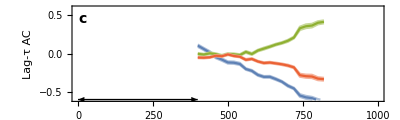

```mathematica
ymin=-0.6;
ymax=0.6;
plotAC=ListLinePlot[{lowerSeries[[;;,{1,2}]],upperSeries[[;;,{1,2}]],meanSeries[[;;,{1,2}]],
lowerSeries[[;;,{1,3}]],upperSeries[[;;,{1,3}]],meanSeries[[;;,{1,3}]],
lowerSeries[[;;,{1,4}]],upperSeries[[;;,{1,4}]],meanSeries[[;;,{1,4}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}}},
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧,
Lighter[TMBcolours⟦3⟧,0.5],Lighter[TMBcolours⟦3⟧,0.5],TMBcolours⟦3⟧,
Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5],TMBcolours⟦4⟧},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Smax

```mathematica
indexStd=Position[ewsStd[[1]],"Smax"][[1,1]];
indexBoot = Position[ewsBoot[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals *)
lowerSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Lower",_}][[;;,{1,3}]];
upperSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Upper",_}][[;;,{1,3}]];
meanSeries=Cases[ewsBoot[[2;;,{1,2,indexBoot}]],{_,"Mean",_}][[;;,{1,3}]];
```

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

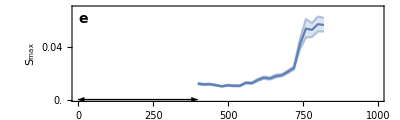

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=0;
ymax=0.07;
plotSmax=ListLinePlot[{lowerSeries,upperSeries,meanSeries},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
FrameLabel->{{"S_max",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[ymin,ymax,0.02],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### AIC

```mathematica
indexStd=Position[ewsStd[[1]],#][[1,1]]&/@{"AIC fold","AIC hopf", "AIC null"};
indexBoot = Position[ewsBoot[[1]],#][[1,1]]&/@{"AIC fold","AIC hopf", "AIC null"};
```

```mathematica
indexStd
```

{10,11,12}

```mathematica
(* Extract confidence intervals *)
lowerSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Lower",_,_,_}][[;;,{1,3,4,5}]];
upperSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Upper",_,_,_}][[;;,{1,3,4,5}]];
meanSeries=Cases[ewsBoot[[2;;,Join[{1,2},indexBoot]]],{_,"Mean",_,_,_}][[;;,{1,3,4,5}]];
```

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],{"ω_fold","ω_hopf"},Spacings->{0,0.1}]
```

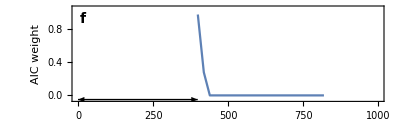

```mathematica
(* Fold AIC from original time-series *)
ymin=-0.05;
ymax=1.05;
plotAIC=ListLinePlot[DeleteCases[ewsStd[[2;;,{2,indexStd[[1]]}]],{_,""}],
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"AIC weight",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->TMBcolours[[1]],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

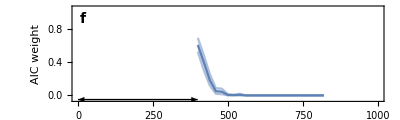

```mathematica
(* Fold AIC weight intervals *)
ymin=-0.05;
ymax=1.05;
plotAIC=ListLinePlot[{lowerSeries[[;;,{1,2}]],upperSeries[[;;,{1,2}]],meanSeries[[;;,{1,2}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2}}},
FrameLabel->{{"AIC weight",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

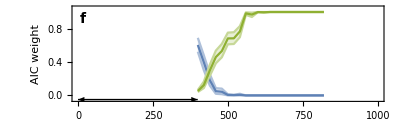

```mathematica
(* Fold AIC weight intervals *)
ymin=-0.05;
ymax=1.05;
plotAIC=ListLinePlot[{lowerSeries[[;;,{1,2}]],upperSeries[[;;,{1,2}]],meanSeries[[;;,{1,2}]],
lowerSeries[[;;,{1,3}]],upperSeries[[;;,{1,3}]],meanSeries[[;;,{1,3}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
FrameLabel->{{"AIC weight",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧,
Lighter[TMBcolours⟦3⟧,0.5],Lighter[TMBcolours⟦3⟧,0.5],TMBcolours⟦3⟧},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

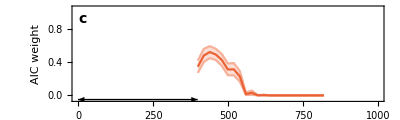

```mathematica
(* Null AIC weight *)
ymin=-0.05;
ymax=1.05;
plotAICNull=ListLinePlot[{lowerSeries[[;;,{1,4}]],upperSeries[[;;,{1,4}]],meanSeries[[;;,{1,4}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{3->{1},3->{2}}},
FrameLabel->{{"AIC weight",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5],TMBcolours⟦4⟧},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Power Spectrum of original series

```mathematica
specData//Dimensions
```

{903,3}

```mathematica
specData[[1]]
```

{Time,Frequency,Empirical}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,1]]];
```

```mathematica
plotTimes
```

{399.,419.,439.,459.,479.,499.,519.,539.,559.,579.,599.,619.,639.,659.,679.,699.,719.,739.,759.,779.,799.,819.}

```mathematica
pspecs=Table[
Cases[specData,
{i,_,_}]⟦;;,{2,3}⟧,
{i,plotTimes}];
```

```mathematica
pspecs//Dimensions
```

{22,41,2}

```mathematica
(* loop power spectrum for display *)
ωVals=pspecs[[1,;;,1]];
ωValsExt={ωVals-2Pi,ωVals,ωVals+2Pi}//Flatten;
pspecsExt=Table[
Transpose[{ωValsExt,Join[pspecs[[i,;;,2]],pspecs[[i,;;,2]],pspecs[[i,;;,2]]]}],
{i,1,Length[pspecs]}];

(* now trim values *)
len=Dimensions[pspecsExt][[2]];
pspecsExt=pspecsExt[[;;,20;;-20]];
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

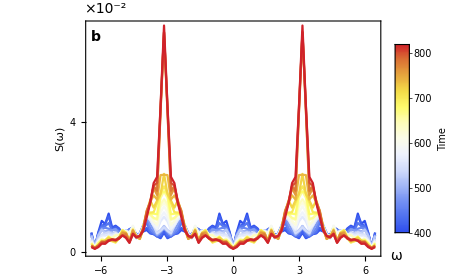

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
plotPspec=ListLinePlot[pspecsExt,
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{2*padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-2",14],Scaled[{0.065,1.05}]],
Text[Style["b",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,20,2]*10^(-2),Range[0,20,2]}],None},{Automatic,None}},
PlotLegends->Placed[colLegend,Scaled[{0.91,0.58}]]]
```

### Power Spectrum of a sampled series

```mathematica
specDataBoot//Dimensions
```

{903,3}

```mathematica
specData[[1]]
```

{Time,Frequency,Empirical}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specDataBoot[[2;;,1]]];
```

```mathematica
plotTimes
```

{399.,419.,439.,459.,479.,499.,519.,539.,559.,579.,599.,619.,639.,659.,679.,699.,719.,739.,759.,779.,799.,819.}

```mathematica
pspecs=Table[
Cases[specDataBoot,
{i,_,_}]⟦;;,{2,3}⟧,
{i,plotTimes}];
```

```mathematica
pspecs//Dimensions
```

{22,41,2}

```mathematica
(* loop power spectrum for display *)
ωVals=pspecs[[1,;;,1]];
ωValsExt={ωVals-2Pi,ωVals,ωVals+2Pi}//Flatten;
pspecsExt=Table[
Transpose[{ωValsExt,Join[pspecs[[i,;;,2]],pspecs[[i,;;,2]],pspecs[[i,;;,2]]]}],
{i,1,Length[pspecs]}];

(* now trim values *)
len=Dimensions[pspecsExt][[2]];
pspecsExt=pspecsExt[[;;,20;;-20]];
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

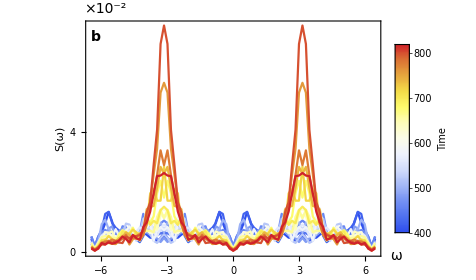

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
plotPspecBoot=ListLinePlot[pspecsExt,
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{2*padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-2",14],Scaled[{0.065,1.05}]],
Text[Style["b",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,20,2]*10^(-2),Range[0,20,2]}],None},{Automatic,None}},
PlotLegends->Placed[colLegend,Scaled[{0.91,0.58}]]]
```

## Grid: Single EWS

```mathematica
gridPlot=Grid[{{bifTrajX,plotPspec},{plotVar,plotSmax},{plotAC,plotAIC},{},{}},Spacings->{-1.5,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 | 
 |

```mathematica
(* Export grid plot *)
Export["figures/bootstrap_final/ews_flip.png",gridPlot,ImageResolution->200];
```